```mathematica
f1 = x + y + 1/x/y + m/x-1/u
```

-1/u+m/x+x+1/(x y)+y

```mathematica
mc = {x->1/2/u + (b Y-a/2)/(X+c), y->a/(X+c)};
```

```mathematica
f1/.mc//Factor;
a1 = Numerator[%]
```

a c^2-2 a^2 c u+a^3 u^2-4 c^3 u^2-4 a c^2 m u^2+2 a c X-2 a^2 u X-12 c^2 u^2 X-8 a c m u^2 X+a X^2-12 c u^2 X^2-4 a m u^2 X^2-4 u^2 X^3-4 a b^2 u^2 Y^2

```mathematica
Series[a1, {X, 0, 8}]
```

(a c^2-2 a^2 c u+a^3 u^2-4 c^3 u^2-4 a c^2 m u^2-4 a b^2 u^2 Y^2)+(2 a c-2 a^2 u-12 c^2 u^2-8 a c m u^2) X+(a-12 c u^2-4 a m u^2) X^2-4 u^2 X^3+O[X]^9

Coefficient of Y^2 ->  -4 a b^2 u^2
Coefficient of X^3 ->-4 u^2
Coefficient of X^2 -> a-12 c u^2-4 a m u^2

```mathematica
s1=Solve[{a-12 c u^2-4 a m u^2==0, -4 u^2/(-4 a b^2 u^2)==-4}, {a, c}]
```

{{a→-1/(4 b^2),c→-(1-4 m u^2)/(48 b^2 u^2)}}

```mathematica
Series[a1/u^2, {X, 0, 8}]/.First@s1//FullSimplify
Coefficient[%, Y^2]
```

((-1+4 u^2 (3 m+9 u-12 m^2 u^2-36 m u^3+2 (-27+8 m^3) u^4))/(13824 b^6 u^6)+Y^2)+((1+8 u^2 (-3 u+m (-1+2 m u^2))) X)/(192 b^4 u^4)-4 X^3+O[X]^9

1

Marino’s claim
b -> 1/(6 Sqrt[2] u)

```mathematica
First@s1/.{b->1/(6 Sqrt[2] u)}
```

{a→-18 u^2,c→-3/2 (1-4 m u^2)}

```mathematica
s2={a->-18 u^2,c->-3/2 (1-4 m u^2), b->1/(6 Sqrt[2] u)}
```

{a→-18 u^2,c→-3/2 (1-4 m u^2),b→1/(6 √2 u)}

```mathematica
a2 = a1/u^2/.s2//Expand
```

-27+324 m u^2+972 u^3-1296 m^2 u^4-3888 m u^5-5832 u^6+1728 m^3 u^6+27 X-216 m u^2 X-648 u^3 X+432 m^2 u^4 X-4 X^3+Y^2

```mathematica
g2 = Coefficient[a2, X]//Simplify
g3 = a2/.{Y->0, X->0}//Simplify
```

27 (1-8 m u^2-24 u^3+16 m^2 u^4)

27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)

```mathematica
disc = g2^3-27g3^2//Simplify
delt = %/(34012224 u^8)//Simplify
```

34012224 u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
delt/.{u^4->u4}
Solve[%==0, u4]
```

m+u-8 m^2 u^2-36 m u^3-27 u4+16 m^3 u4

{{u4→(-m-u+8 m^2 u^2+36 m u^3)/(-27+16 m^3)}}

```mathematica
disc0sol = {u^p_:>((-m-u+8 m^2 u^2+36 m u^3)/(-27+16 m^3))u^(p-4)/;p>=4};
```

```mathematica
delt/.disc0sol//Simplify
```

0

```mathematica
4(x-x0)^2(x-x1)//Expand
%/.{x->0}/.{x1->-2x0}
```

4 x^3-8 x^2 x0+4 x x0^2-4 x^2 x1+8 x x0 x1-4 x0^2 x1

8 x0^3

```mathematica
4 x0^2+8 x0 x1/.{x1->-2x0}
```

-12 x0^2

```mathematica
X0sol = {X0->-3/2 g3/g2}
```

{X0→-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
4(X-X0)^2(X-X1)/.{X->t^2-2X0}//Simplify
```

4 (t^2-3 X0)^2 (t^2-2 X0-X1)

Marcos eq 1.9

```mathematica
node = Y^2-4(X-X0)^2(X-X1)//Expand;
```

```mathematica
param = {X->t^2-2X0, Y->2t(t^2-3X0)}
```

{X→t^2-2 X0,Y→2 t (t^2-3 X0)}

```mathematica
node/.{X1->-2X0}/.param//Simplify
```

0

```mathematica
p2 = param/.{t->t/Sqrt[2]}//Simplify
```

{X→1/2 (t^2-4 X0),Y→(t (t^2-6 X0))/(√2)}

```mathematica
{x, y}/.mc/.s2
%/.p2//Simplify
```

{1/(2 u)+(9 u^2+Y/(6 √2 u))/(-3/2 (1-4 m u^2)+X),-(18 u^2)/(-3/2 (1-4 m u^2)+X)}

{(-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0)/(6 u (-3+t^2+12 m u^2-4 X0)),-(36 u^2)/(-3+t^2+12 m u^2-4 X0)}

```mathematica
rule = Thread[{u^4, u^5, u^6, u^7}->FixedPoint[Simplify[Expand[#]/.disc0sol]&, {u^4, u^5, u^6, u^7}]]
```

{u^4→(m+u-8 m^2 u^2-36 m u^3)/(27-16 m^3),u^5→(-9 m u-16 m^4 u+27 u^2+272 m^3 u^2+128 m^5 u^3+36 m^2 (-1+30 u^3))/((27-16 m^3)^2),u^6→(-108 m^2 u-704 m^5 u+243 m u^2+8928 m^4 u^2+768 m^7 u^2-729 u^3+128 m^6 (-1+70 u^3)+216 m^3 (-5+148 u^3))/((-27+16 m^3)^3),u^7→1/((27-16 m^3)^4)(729 u-2808 m^3 u-22784 m^6 u-2048 m^9 u-2916 m^2 u^2+273024 m^5 u^2+60416 m^8 u^2+12288 m^10 u^3-729 m (-1+45 u^3)+256 m^7 (-35+1737 u^3)+432 m^4 (-74+2115 u^3))}

```mathematica
Solve[tsq1==3-12 m u^2+4 X0, X0]/.{tsq1->t1^2}
-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0/.First@%//FullSimplify
%/.{u^3->(m+u-8 m^2 u^2-27 u^4+16 m^3 u^4)/(36 m)}//FullSimplify//Expand
```

{{X0→1/4 (-3+t1^2+12 m u^2)}}

3 t^2+t^3-3 t1^2+108 u^3-3/2 t (-3+t1^2+12 m u^2)

3+(9 t)/2+3 t^2+t^3-3 t1^2-(3 t t1^2)/2+(3 u)/m-24 m u^2-18 m t u^2-(81 u^4)/m+48 m^2 u^4

#### Brute force

```mathematica
msol = Solve[t1==-2+Sqrt[1+12m u^2], m]
delt/.First[%]//FullSimplify
Numerator[%]/.{u^3->u3}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{m→(3+4 t1+t1^2)/(12 u^2)}}

((t1^2 (3+t1)-54 u^3) ((1+t1) (4+t1)^2+54 u^3))/(108 u^2)

(t1^2 (3+t1)-54 u3) ((1+t1) (4+t1)^2+54 u3)

```mathematica
u3sol = Solve[(t1^2 (3+t1)-54 u3) ((1+t1) (4+t1)^2+54 u3)==0, u3]
```

{{u3→1/54 t1^2 (3+t1)},{u3→-1/54 (1+t1) (4+t1)^2}}

```mathematica
X0/.X0sol/.First[msol]/.{u^3->u3,u^4->u3 u,u^5->u3 u^2,u^6->u3^2}/.u3sol;
%//ExpandAll//FullSimplify
```

{1/2 t1 (2+t1),1/2 (2+t1) (4+t1)}

```mathematica
-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0/.First[msol]/.{X0->t1^2/2+t1}/.{u^3->u3}/.u3sol//FullSimplify//Factor
```

{(t-t1)^2 (3+t+2 t1),-32+3 t^2+t^3-48 t1-6 t t1-21 t1^2-3 t t1^2-2 t1^3}

```mathematica
(t-t1)^2(t+3+2t1)//Expand
```

3 t^2+t^3-6 t t1+3 t1^2-3 t t1^2+2 t1^3

#### Proof of equivalence of the expression above and eq (1.11-15) Marino

```mathematica
tsq=3-12 m u^2+4 X0/.X0sol//Simplify
```

-(9 (-1+32 u^3-48 m^2 u^4-144 u^6+64 m^3 u^6-4 m u^2 (-3+32 u^3)))/(1-8 m u^2-24 u^3+16 m^2 u^4)

```mathematica
(-2+Sqrt[1+12m u^2])^2//Expand
(t1^2-%)/.{Sqrt[1+12m u^2]->sq}
Expand[sq^2/.First@Solve[%==0, sq]]
t1eqn = -16(1+12m u^2-%)//Simplify
```

5+12 m u^2-4 √(1+12 m u^2)

-5+4 sq+t1^2-12 m u^2

25/16-(5 t1^2)/8+t1^4/16+(15 m u^2)/2-3/2 m t1^2 u^2+9 m^2 u^4

t1^4+9 (1-4 m u^2)^2-2 t1^2 (5+12 m u^2)

```mathematica
t1eqn/.{t1^2->tsq, t1^4->tsq^2}//FullSimplify
Assuming[delt==0, FullSimplify[%]]
```

(576 u^2 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4) (-1+4 u^2 (3 m+6 u-12 m^2 u^2-24 m u^3+(-27+16 m^3) u^4)))/((1+8 u^2 (-3 u+m (-1+2 m u^2)))^2)

0

```mathematica
-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0/.X0sol//FullSimplify
```

1/(1+8 u^2 (-3 u+m (-1+2 m u^2)))((-3+t) (3+t)^2-4 m (3+t) (-27+2 t^2) u^2-12 (3+t) (-27+2 t^2) u^3+16 m^2 (3+t) (-27+t^2) u^4-432 m (10+3 t) u^5+72 (8 m^3 (3+t)-9 (10+3 t)) u^6+1728 m^2 u^7)

```mathematica
(t+3+2t1)(t-t1)^2/.{t1->-2+Sqrt[1+12m u^2]}//Expand
```

-13-3 t+3 t^2+t^3-108 m u^2-36 m t u^2+14 √(1+12 m u^2)+6 t √(1+12 m u^2)+24 m u^2 √(1+12 m u^2)

```mathematica
X0/.X0sol
```

-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))

```mathematica
Assuming[delt==0, FullSimplify[X0/.X0sol]]
```

(3+12 u^2 (-2 m-8 u+4 m^2 u^2+27 u^4))/(2+16 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
Solve[-3+t^2+12 m u^2-4 X0==0, t]
```

{{t→-√(3-12 m u^2+4 X0)},{t→√(3-12 m u^2+4 X0)}}

X0 with disc0 applied many times doesn’t seem to simplify it to eq. (1.15)

```mathematica
X0/.X0sol
%/.disc0sol//FullSimplify
%/.disc0sol//FullSimplify
%/.disc0sol//FullSimplify
%/.disc0sol//FullSimplify
```

-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))

(-81+12 (-8 m^3-48 m^2 u+m (-9+64 m^3) u^2+(189+592 m^3) u^3+64 m^2 (27-2 m^3) u^4+72 m (27-8 m^3) u^5))/(-54+16 u (-2 m^2+27 m u+3 (27+8 m^3) u^2))

(2187+12 (-1620 m^3-8 m^2 (297+8 m^3) u+27 m (-63+464 m^3) u^2+(-5103+64800 m^3+256 m^6) u^3-2592 m^2 (-27+8 m^3) u^4))/(2 (-27+16 m^3) (-27+8 u (-2 m^2+27 m u+3 (27+8 m^3) u^2)))

(-59049+12 (-2592 m^3 (9+2 m^3)-8 m^2 (729+1944 m^3+128 m^6) u+27 m (1701+160 m^3 (45+8 m^3)) u^2+(137781+688176 m^3+283392 m^6+4096 m^9) u^3))/(2 (27-16 m^3)^2 (-27+8 u (-2 m^2+27 m u+3 (27+8 m^3) u^2)))

(-59049+12 (-2592 m^3 (9+2 m^3)-8 m^2 (729+1944 m^3+128 m^6) u+27 m (1701+160 m^3 (45+8 m^3)) u^2+(137781+688176 m^3+283392 m^6+4096 m^9) u^3))/(2 (27-16 m^3)^2 (-27+8 u (-2 m^2+27 m u+3 (27+8 m^3) u^2)))

Trying a numerical check to understand

```mathematica
delt
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
eg = {m->.4+.3I};
egsol =Solve[(delt/.eg)==0, u]
{-√(3-12 m u^2+4 X0)/.X0sol/.eg/.%, -2+Sqrt[1+12m u^2]/.eg/.%, -2-Sqrt[1+12m u^2]/.eg/.%, 3(4m u^2+18u^3-1)/(12m u^2+1)/.eg/.egsol}//TableForm
```

{{u→-0.34906-0.33296 ⅈ},{u→-0.24047-0.317484 ⅈ},{u→-0.196609+0.248607 ⅈ},{u→0.294943-0.02119 ⅈ}}

-2.83402-0.692593 ⅈ | -1.33982+0.437928 ⅈ | -0.860026-0.242363 ⅈ | -0.787088+0.103698 ⅈ
-1.16598+0.692593 ⅈ | -1.33982+0.437928 ⅈ | -0.860026-0.242363 ⅈ | -0.787088+0.103698 ⅈ
-2.83402-0.692593 ⅈ | -2.66018-0.437928 ⅈ | -3.13997+0.242363 ⅈ | -3.21291-0.103698 ⅈ
-2.83402-0.692593 ⅈ | -1.33982+0.437928 ⅈ | -0.860026-0.242363 ⅈ | -0.787088+0.103698 ⅈ

```mathematica
t1sol = {t1->-2+Sqrt[1+12m u^2]};
```

```mathematica
{X0/.X0sol/.eg/.egsol, (t1^2+2t1)/2/.t1sol/.eg/.egsol, 3(48m^2u^4-16m u^2-36u^3+1)/(24m u^2+2)/.eg/.egsol}//TableForm
```

0.94197+1.27023 ⅈ | -0.538151-0.148817 ⅈ | -0.519574-0.0339246 ⅈ | -0.482711+0.0220786 ⅈ
-0.726068-0.114957 ⅈ | -0.538151-0.148817 ⅈ | -0.519574-0.0339246 ⅈ | -0.482711+0.0220786 ⅈ
0.94197+1.27023 ⅈ | -0.538151-0.148817 ⅈ | -0.519574-0.0339246 ⅈ | -0.482711+0.0220786 ⅈ

```mathematica
2.8340188217282782-(-1.1659811782717218)
```

4.

```mathematica
Solve[-3+t^2+12 m u^2-4 X0==0, t]
```

{{t→-√(3-12 m u^2+4 X0)},{t→√(3-12 m u^2+4 X0)}}

```mathematica
(t-√(3-12 m u^2+4 X0))^2(t+3+2 √(3-12 m u^2+4 X0))//Expand
%-(-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0)//FullSimplify
```

9-9 t+3 t^2+t^3-36 m u^2+36 m t u^2+12 X0-12 t X0+6 √(3-12 m u^2+4 X0)-6 t √(3-12 m u^2+4 X0)-24 m u^2 √(3-12 m u^2+4 X0)+8 X0 √(3-12 m u^2+4 X0)

-108 u^3-24 m u^2 (3+√(3-12 m u^2+4 X0))+2 (3+4 X0) (3+√(3-12 m u^2+4 X0))-3 t (3-12 m u^2+2 X0+2 √(3-12 m u^2+4 X0))

```mathematica
With[{t1=-2+Sqrt[1+12m u^2]}, Simplify[(t1^2+2t1)/2]]
```

1/2+6 m u^2-√(1+12 m u^2)

```mathematica
(t-t1)^2(t+3+2t1)-(-9+3 t^2+t^3+36 m u^2+108 u^3-12 X0-6 t X0)//Expand
CoefficientList[%, t]
```

9-6 t t1+3 t1^2-3 t t1^2+2 t1^3-36 m u^2-108 u^3+12 X0+6 t X0

{9+3 t1^2+2 t1^3-36 m u^2-108 u^3+12 X0,-6 t1-3 t1^2+6 X0}

```mathematica
{1/6/u(t+3+2t1)(t-t1)/(t+t1), -36u^2/(t^2-t1^2)}/.t1sol//Expand//Simplify
```

{(-4+t+t^2-24 m u^2+5 √(1+12 m u^2)+t √(1+12 m u^2))/(6 u (-2+t+√(1+12 m u^2))),-(36 u^2)/(t^2-(-2+√(1+12 m u^2))^2)}

```mathematica
Solve[t1^2+2t1-2X0==0/.X0sol, t1]//Simplify;
%/.disc0sol//Simplify
```

{{t1→-1-2 √((-27+729 u^3-384 m^5 u^4-192 m^4 u^2 (-1+9 u^3)+24 m^3 (-1+76 u^3)+4 m^2 u (-37+1296 u^3)+27 m (u^2+216 u^5))/(-27-16 m^2 u+216 m u^2+648 u^3+192 m^3 u^3))},{t1→-1+2 √((-27+729 u^3-384 m^5 u^4-192 m^4 u^2 (-1+9 u^3)+24 m^3 (-1+76 u^3)+4 m^2 u (-37+1296 u^3)+27 m (u^2+216 u^5))/(-27-16 m^2 u+216 m u^2+648 u^3+192 m^3 u^3))}}

```mathematica
u^4/.disc0sol
```

(-m-u+8 m^2 u^2+36 m u^3)/(-27+16 m^3)

```mathematica
disc0sol
```

{u^p_:>((-m-u+8 m^2 u^2+36 m u^3) u^(p-4))/(-27+16 m^3)/;p≥4}

```mathematica
X0/.X0sol
```

-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))

```mathematica
2-16 m u^2-48 u^3+32 m^2 u^4/.{u^4->(-m-u+8 m^2 u^2+36 m u^3)/(-27+16 m^3)}//FullSimplify
```

(-54+16 u (-2 m^2+27 m u+3 (27+8 m^3) u^2))/(-27+16 m^3)

assuming Marcos’s eq 1.11 is verified

```mathematica
ratF1 = {x->1/6/u(t+3+2t1)(t-t1)/(t+t1), y->-36u^2/(t^2-t1^2)}
```

{x→((t-t1) (3+t+2 t1))/(6 (t+t1) u),y→-(36 u^2)/(t^2-t1^2)}

```mathematica
t1Ratsol = {t1->3(4m u^2+18u^3-1)/(12m u^2+1)}//Simplify
```

{t1→(3 (-1+4 m u^2+18 u^3))/(1+12 m u^2)}

```mathematica
t1^2/2+t1/.t1Ratsol//Simplify
```

(3 (-1+4 m u^2+18 u^3) (-1+36 m u^2+54 u^3))/(2 (1+12 m u^2)^2)

```mathematica
repz = {z->(t-Sqrt[6X0])/(t+Sqrt[6X0])};
```

```mathematica
tToz = First@Solve[(z/.repz)==z, t]//Simplify
```

{t→-(√6 √X0 (1+z))/(-1+z)}

```mathematica
x/.ratF1/.tToz//Factor
```

-((-3-2 t1-√6 √X0+3 z+2 t1 z-√6 √X0 z) (-t1+√6 √X0+t1 z+√6 √X0 z))/(6 u (-1+z) (-t1-√6 √X0+t1 z-√6 √X0 z))

```mathematica
Solve[-3-2 t1-√6 √X0+3 z+2 t1 z-√6 √X0 z==0, z]
```

{{z→(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0)}}

```mathematica
Solve[-t1+√6 √X0+t1 z+√6 √X0 z==0, z]
```

{{z→(t1-√6 √X0)/(t1+√6 √X0)}}

```mathematica
Solve[(-t1-√6 √X0+t1 z-√6 √X0 z)==0, z]
```

{{z→(t1+√6 √X0)/(t1-√6 √X0)}}

```mathematica
y/.ratF1/.tToz/.{X0->w^2}//Factor
```

(36 u^2 (-1+z)^2)/(t1^2-6 w^2-2 t1^2 z-12 w^2 z+t1^2 z^2-6 w^2 z^2)

```mathematica
Solve[t1^2-6 w^2-2 t1^2 z-12 w^2 z+t1^2 z^2-6 w^2 z^2==0, z]//Cancel
```

{{z→(t1^2-2 √6 t1 w+6 w^2)/(t1^2-6 w^2)},{z→(t1^2+2 √6 t1 w+6 w^2)/(t1^2-6 w^2)}}

```mathematica
Solve[t1^2-6 X0-2 t1^2 z-12 X0 z+t1^2 z^2-6 X0 z^2==0, z]
```

{{z→(t1^2-2 √6 t1 √X0+6 X0)/(t1^2-6 X0)},{z→(t1^2+2 √6 t1 √X0+6 X0)/(t1^2-6 X0)}}

```mathematica
Cancel[(t1^2-2 √6 t1 √X0+6 X0)/(t1^2-6 X0)]
```

(t1^2-2 √6 t1 √X0+6 X0)/(t1^2-6 X0)

```mathematica
eq126 = {a->(3+2t1+Sqrt[6X0])/(3+2t1-Sqrt[6X0]), b->(t1-Sqrt[6X0])/(t1+Sqrt[6X0]), c->1/b, d->1};
```

```mathematica
Block[{a,b,c,d, alp, bet, dd, ee},
Evaluate[Array[alp, 4]] = {a,b,c,d};
Evaluate[Array[dd, 4]] = {1, 1, -1, -1};
Evaluate[Array[bet, 3]] = {d, b, c};
Evaluate[Array[ee, 3]] = {2, -1, -1};
Sum[dd[j]ee[k]D2[alp[j]/bet[k]], {j, 1, 4}, {k, 1, 3}]//Simplify
]/.{a->1/b^2, c->1/b, d->1}//Simplify
%/.D2[b^n_]:>-D2[b^-n]/;n<0/.D2[1]->0
```

-2 D2[1]-D2[1/b^3]+3 D2[1/b^2]-2 D2[1/b]+3 D2[b]-D2[b^2]

5 D2[b]-4 D2[b^2]+D2[b^3]

```mathematica
dvec={1,1,-1,-1};evec={2,-1,-1};avec={a,b,c,d};bvec={d,b,c};
A=Sum[dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]],{j,Length[dvec]},{k,Length[evec]}]/.{d->1,c->1/b,a->1/b^2}
```

-2 BW[1]-BW[1/b^3]+3 BW[1/b^2]-2 BW[1/b]+3 BW[b]-BW[b^2]

```mathematica
B3 = Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;
B3 = B3 + Log[Xatinf1]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}];
B3 = B3/.{d->1,c->1/b,a->1/b^2}//Simplify
```

-Li2[1/b^3]+Li2[1/b^2]+Li2[b]-Li2[b^2]+2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])-Log[1-b] Log[1/b]-(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]-2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])-Log[1-1/b^3] (Log[1/b^2]-Log[b])+Log[1-1/b^2] (Log[1/b]-Log[b])-Log[(-1+b)/b] Log[b]+2 (Li2[b]+Log[1-b] Log[b])+(Log[1/b]-Log[b]) Log[1-b^2]-(Log[1/b]+Log[b]) Log[Xatinf1]

```mathematica
evec
bvec/.{d->1,c->1/b,a->1/b^2}
```

{2,-1,-1}

{1,b,1/b}

```mathematica
A1 = A/.{BW[1]->0}
```

-BW[1/b^3]+3 BW[1/b^2]-2 BW[1/b]+3 BW[b]-BW[b^2]

```mathematica
A1+I B3/.{BW[z_]:>(Li2[z]-Li2[Conjugate[z]])/2/I+((Log[1-z]-Log[1-Conjugate[z]])/2/I)((Log[z]+Log[Conjugate[z]])/2)};
%/.{Conjugate[b]->1/b};
%/.{Li2[Power[b, n_]]:>-Li2[b^-n]-Pi^2/6-1/2Log[-b^-n]^2/;n<0}//Simplify
A100 = Assuming[0<b<1, FullSimplify[%]]
%/.{b->Exp[2Pi I/3]}//Simplify
```

-1/12 ⅈ (2 π^2+27 Log[1-b] Log[1/b]+12 Log[1/b^2] Log[(-1+b)/b]-3 Log[1/b] Log[(-1+b)/b]+3 Log[-b]^2-9 Log[1-b] Log[b]-3 Log[(-1+b)/b] Log[b]+6 Log[-b^2]^2-12 Log[1-1/b^2] (Log[1/b^2]+Log[1/b]-Log[b]-Log[b^2])-3 Log[-b^3]^2-3 Log[1-1/b^3] (Log[1/b^3]-4 Log[1/b^2]+4 Log[b]+Log[b^3])-12 Log[1/b^2] Log[1-b^2]-12 Log[1/b] Log[1-b^2]+12 Log[b] Log[1-b^2]-12 Log[b^2] Log[1-b^2]+3 Log[1/b^3] Log[1-b^3]+3 Log[b^3] Log[1-b^3]+12 Log[1/b] Log[Xatinf1]+12 Log[b] Log[Xatinf1])

1/3 ⅈ (π^2+3 Log[b] (-2 ⅈ π+Log[b]-8 Log[1+b]+3 Log[1+b+b^2]))

Simplify::infd: Expression Log[1+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)] simplified to -∞.

Simplify::infd: Expression -2 Log[1+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)] simplified to ∞.

Simplify::infd: Expression 3 ⅈ π-2 Log[1+ⅇ^(-(2 ⅈ π)/3)+ⅇ^((2 ⅈ π)/3)] simplified to ∞.

General::stop: Further output of Simplify::infd will be suppressed during this calculation.

∞

```mathematica
A100/.{b->Exp[2Pi I /3]}//Simplify
```

∞

```mathematica
Limit[Log[b]-8 Log[1+b]+3 Log[1+b+b^2], b->Exp[2Pi I/3]]
```

Limit::ztest1: Unable to decide whether numeric quantity 1-(-1)^(1/3)+(-1)^(2/3) is equal to zero. Assuming it is.

-∞

```mathematica
Li2[1/b^2]//FullForm
```

Li2[Power[b,-2]]

```mathematica
Li2[1/b^2]/.{Li2[Power[b, n_]]:>-Li2[b^-n]-Pi^2/6-1/2Log[-b^-n]^2/;n<0}
```

-π^2/6-Li2[b^2]-1/2 Log[-b^2]^2

```mathematica
Li2[1/b^2]//FullForm
```

Li2[Power[b,-2]]

## Weierstrass

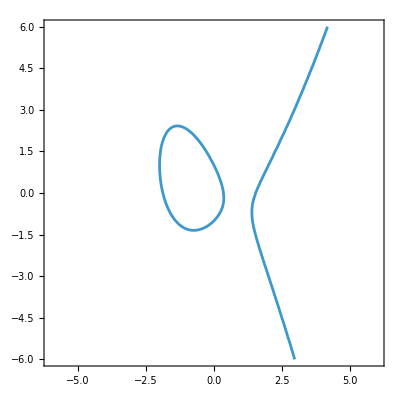

```mathematica
ContourPlot[y^2+x y ==x^3-3x+1, {x, -6, 6}, {y, -6, 6}]
```

```mathematica
x^2 y + x y^2 - x y z/u +m y z^2 + z^3/.{y->y-1/m z}//Expand
%/.{y->a y+r x+s z, x->y+x}//Simplify//Expand
Coefficient[%, {x y^2, x^2 y}]
```

x^2 y+x y^2-(x^2 z)/m-(2 x y z)/m-(x y z)/u+(x z^2)/m^2+(x z^2)/(m u)+m y z^2

r x^3+r^2 x^3+a x^2 y+2 r x^2 y+2 a r x^2 y+r^2 x^2 y+2 a x y^2+a^2 x y^2+r x y^2+2 a r x y^2+a y^3+a^2 y^3-(x^2 z)/m-(2 r x^2 z)/m+s x^2 z+2 r s x^2 z-(r x^2 z)/u-(2 x y z)/m-(2 a x y z)/m-(2 r x y z)/m+2 s x y z+2 a s x y z+2 r s x y z-(a x y z)/u-(r x y z)/u-(y^2 z)/m-(2 a y^2 z)/m+s y^2 z+2 a s y^2 z-(a y^2 z)/u+(x z^2)/m^2+m r x z^2-(2 s x z^2)/m+s^2 x z^2+(x z^2)/(m u)-(s x z^2)/u+(y z^2)/m^2+a m y z^2-(2 s y z^2)/m+s^2 y z^2+(y z^2)/(m u)-(s y z^2)/u+m s z^3

{2 a+a^2+r+2 a r,a+2 r+2 a r+r^2}

```mathematica
x^2 y + x y^2 - x y z/u +m y z^2 + z^3/.{z->1}/.{y->y-1/m}//Simplify//Expand
%/.{x->y,y->x}
Z^3*%/.{x->X/Z, y->Y/Z}//Expand
{F3, F2, F1} = CoefficientList[%, Z]
```

x/m^2+x/(m u)-x^2/m+m y-(2 x y)/m-(x y)/u+x^2 y+x y^2

m x+y/m^2+y/(m u)-(2 x y)/m-(x y)/u+x^2 y-y^2/m+x y^2

X^2 Y+X Y^2-(2 X Y Z)/m-(X Y Z)/u-(Y^2 Z)/m+m X Z^2+(Y Z^2)/m^2+(Y Z^2)/(m u)

{X^2 Y+X Y^2,-(2 X Y)/m-(X Y)/u-Y^2/m,m X+Y/m^2+Y/(m u)}

```mathematica
{s8, s9} = Coefficient[F1, {X, Y}]
```

{m,1/m^2+1/(m u)}

```mathematica
e2 = F2/.{X->s9, Y->-s8}//Expand
```

2/m^2-m+1/u^2+3/(m u)

```mathematica
e3 = F3/.{X->s9, Y->-s8}//Expand
```

1-1/m^3-1/(m u^2)-2/(m^2 u)+m/u

e2, e3 should not simultaneously be 0

```mathematica
ContourPlot[{1-1/m^3-1/(m u^2)-2/(m^2 u)+m/u==0, 2/m^2-m+1/u^2+3/(m u)==0}, {m, -5, 5}, {u, -5, 5}, PlotPoints->100, MaxRecursion->4]
```

$Aborted

at this point we assume generic e3 and proceed TODO: see what happens when e3 = 0

```mathematica
(* check that Q lies on the curve *)
F3 + F2 Z + F1 Z^2/.{X->-e2 s9, Y->e2 s8, Z->e3}//Expand
```

0

```mathematica
(* change of coordinates and check that Q becomes [0, 0, 1] *)
c1 = F3 + F2 Z + F1 Z^2/.{X->X-e2 s9/e3 Z, Y->Y+e2 s8/e3 Z}//Expand;
%/.{X->0, Y->0, Z->1}//Simplify
```

0

```mathematica
c1//Simplify;
{f3, f2, f1} = CoefficientList[%, Z];
```

```mathematica
phi3 = f3/.{X->1, Y->t}//Simplify
```

t (1+t)

```mathematica
phi2 = f2/.{X->1, Y->t}//Simplify
```

-1/(m u (m+u) (m+u-m^3 u))(m^5 (1+t) u-m^2 t (4+3 t) u-m t (5+3 t) u^2+m^4 (3+5 t) u^2-t (2+t) u^3-m^6 (1+2 t) u^3-m^3 (t+t^2-2 u^3-4 t u^3))

```mathematica
phi1 = f1/.{X->1, Y->t}//Simplify
```

(10 m^2 t u^3-3 m^10 u^4+5 m t u^4+m^12 u^5+t u^5+m^9 u^2 (1+2 t-3 u^3)+m^8 (1+t) (-1+6 u^3)+m^5 (t-19 u^3-28 t u^3)+m^4 (5 t u-12 u^4-17 t u^4)+m^3 (10 t u^2-3 u^5-4 t u^5)+m^6 u^2 (-15+4 u^3+2 t (-11+u^3))+m^7 u (-6+9 u^3+t (-8+6 u^3)))/(m^2 u (m+u)^2 (m+u-m^3 u)^2)

```mathematica
delt = phi2^2-4phi1 phi3//Simplify
```

((-m^5 (1+t) u+m^2 t (4+3 t) u+m t (5+3 t) u^2-m^4 (3+5 t) u^2+t (2+t) u^3+m^6 (1+2 t) u^3+m^3 (t+t^2-2 u^3-4 t u^3))^2-4 t (1+t) u (10 m^2 t u^3-3 m^10 u^4+5 m t u^4+m^12 u^5+t u^5+m^9 u^2 (1+2 t-3 u^3)+m^8 (1+t) (-1+6 u^3)+m^5 (t-19 u^3-28 t u^3)+m^4 (5 t u-12 u^4-17 t u^4)+m^3 (10 t u^2-3 u^5-4 t u^5)+m^6 u^2 (-15+4 u^3+2 t (-11+u^3))+m^7 u (-6+9 u^3+t (-8+6 u^3))))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
(* check that phi and delt are defined correctly *)
c2 = c1 /. Z -> 1 /. {X -> x, Y -> y};
% /. {y -> t x} /. {x -> (-phi2 + Sqrt[delt])/2/phi3} // Simplify
```

0

```mathematica
rho = tp^4 * delt/.{t->-s8/s9 + 1/tp}//Simplify
```

(m^2 (10+8 tp+tp^2) u^3-m^8 tp (4+15 tp+12 tp^2) u^3+m (5+2 tp) u^4+4 m^10 tp^2 (2+3 tp) u^4+u^5-4 m^12 tp^3 u^5-2 m^7 tp (1+tp) u (1+4 (1+3 tp) u^3)+m^9 tp^2 u^2 (1+4 (2+3 tp) u^3)-2 m^6 tp u^2 (1+2 u^3+tp^2 (-2+6 u^3)+tp (-2+8 u^3))+m^4 u (5+12 tp^3 u^3+2 tp (4+5 u^3)+3 tp^2 (1+8 u^3))+m^3 u^2 (10+4 tp^3 u^3+4 tp (3+u^3)+tp^2 (3+8 u^3))+m^5 (1+12 tp^3 u^3+tp (2+6 u^3)+tp^2 (1+22 u^3)))/(m^2 u^2 (m+u) (m+u-m^3 u)^2)

```mathematica
c = Coefficient[rho, tp, 3]//Simplify
```

(4 m (m+u-m^3 u))/(m+u)

```mathematica
CoefficientList[rho, tp]//Simplify
```

{(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2),(2 (m+u) (m+u+2 m^2 u^2))/(m u^2 (m+u-m^3 u)),8 m+1/u^2,(4 m (m+u-m^3 u))/(m+u)}

```mathematica
ysq = 4c^2 rho/.{tp->x/c}//Simplify
CoefficientList[%, x]//Simplify
```

(4 (8 u x+x^2+16 m^2 (1+u^2 x)+8 m (4 u+x+u^2 x^2)+u^2 (16+x^3)))/u^2

{(64 (m+u)^2)/u^2,(32 (m+u+2 m^2 u^2))/u^2,4 (8 m+1/u^2),4}

```mathematica
a = Coefficient[ysq, x, 2]
```

(4 (1+8 m u^2))/u^2

```mathematica
ysq/.{x->X-a/12, y->Y}//Expand
CoefficientList[%, X]//Simplify
```

64-(512 m^3)/27+8/(27 u^6)-(32 m)/(9 u^4)-32/(3 u^3)+(128 m^2)/(9 u^2)+(128 m)/(3 u)-(64 m^2 X)/3-(4 X)/(3 u^4)+(32 m X)/(3 u^2)+(32 X)/u+4 X^3

{-(8 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(27 u^6),-(4 (1-8 m u^2-24 u^3+16 m^2 u^4))/(3 u^4),0,4}

## Recheck

```mathematica
x+y+1/x/y+m/x-1/u
x y * %//Expand
%/.{y->y-1/m}//Expand
%/.{x->y,y->x}
F = Z^3 * %/.{x->X/Z, y->Y/Z}//Expand
{F3, F2, F1} = Simplify@CoefficientList[%, Z]
```

-1/u+m/x+x+1/(x y)+y

1+m y-(x y)/u+x^2 y+x y^2

x/m^2+x/(m u)-x^2/m+m y-(2 x y)/m-(x y)/u+x^2 y+x y^2

m x+y/m^2+y/(m u)-(2 x y)/m-(x y)/u+x^2 y-y^2/m+x y^2

X^2 Y+X Y^2-(2 X Y Z)/m-(X Y Z)/u-(Y^2 Z)/m+m X Z^2+(Y Z^2)/m^2+(Y Z^2)/(m u)

{X Y (X+Y),-(Y (m X+u (2 X+Y)))/(m u),(m^3 X+Y+(m Y)/u)/m^2}

```mathematica
F1
{A, B} = Simplify@Coefficient[%, {X, Y}]
```

(m^3 X+Y+(m Y)/u)/m^2

{m,(m+u)/(m^2 u)}

```mathematica
e2 = F2/.{X->B, Y->-A}//Simplify
```

2/m^2-m+1/u^2+3/(m u)

```mathematica
e3 = F3/.{X->B, Y->-A}//Simplify
```

((m+u) (-m-u+m^3 u))/(m^3 u^2)

```mathematica
Qcoords = Simplify@{-e2 B, e2 A, e3}
```

{((m+u) (-m^2-3 m u-2 u^2+m^3 u^2))/(m^4 u^3),2/m-m^2+m/u^2+3/u,((m+u) (-m-u+m^3 u))/(m^3 u^2)}

```mathematica
F1/.Thread[{X,Y,Z}->Qcoords]//Simplify
```

0

```mathematica
F/.Thread[{X,Y,Z}->Qcoords]//Simplify
```

0

```mathematica
Solve[2/m^2-m+1/u^2+3/(m u)==0, u]
```

{{u→(-3 m+√(m^2+4 m^5))/(2 (2-m^3))},{u→(3 m+√(m^2+4 m^5))/(2 (-2+m^3))}}

```mathematica
Solve[{((m+u) (u-(m+u)/m^3))/u^2==0}, {u}]
e2/.%//Simplify
```

{{u→-m},{u→m/(-1+m^3)}}

{-m,m^4}

```mathematica
<<MaTeX`;
texStyle={FontSize->12, FontFamily->"Times New Roman"}; 
SetOptions[MaTeX,FontSize->12,"Preamble"->{"\\usepackage[english]{babel}","\\usepackage{amsmath,amssymb}", "\\usepackage{lmodern}"}];
imgWidth=218;
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
```

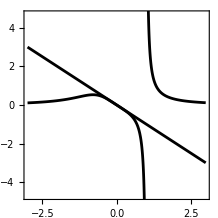

/Users/rishi/Developer/localf1/figures/e3Vanish.pdf

```mathematica
plt1 = ParametricPlot[{{m, -m}, {m, m/(-1+m^3)}}, {m, -3, 3},
BaseStyle->texStyle,
AspectRatio->1,
PlotStyle->Black,
Frame->True,
FrameLabel->MaTeX/@{"m", "u"},
ImageSize->imgWidth
]
(*Export["/Users/rishi/Developer/localf1/figures/e3Vanish.pdf", plt1]*)
```

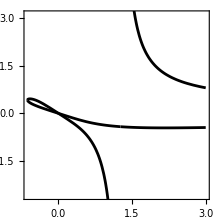

/Users/rishi/Developer/localf1/figures/e2Vanish.pdf

```mathematica
plt2 = ParametricPlot[{{m, (-3 m+√(m^2+4 m^5))/(2 (2-m^3))}, {m, (3 m+√(m^2+4 m^5))/(2 (-2+m^3))}}, {m, -3, 3},
BaseStyle->texStyle,
AspectRatio->1,
PlotStyle->Directive[Black],
Frame->True,
FrameLabel->MaTeX/@{"m", "u"},
ImageSize->imgWidth
]
(*Export["/Users/rishi/Developer/localf1/figures/e2Vanish.pdf", plt2]*)
```

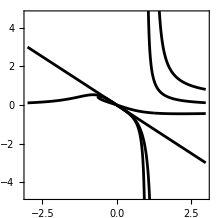

```mathematica
Show[plt1, plt2]
```

```mathematica
FullSimplify[F/.{X->Xp-B e2/e3 Zp, Y->Yp+A e2/e3 Zp, Z->Zp}]
{f3p, f2p, f1p} = FullSimplify/@CoefficientList[%, Zp]
```

(m^6 u Xp^2 Yp+4 m^5 u^2 Xp^2 Yp-2 m^8 u^2 Xp^2 Yp+6 m^4 u^3 Xp^2 Yp-6 m^7 u^3 Xp^2 Yp+m^10 u^3 Xp^2 Yp+4 m^3 u^4 Xp^2 Yp-6 m^6 u^4 Xp^2 Yp+2 m^9 u^4 Xp^2 Yp+m^2 u^5 Xp^2 Yp-2 m^5 u^5 Xp^2 Yp+m^8 u^5 Xp^2 Yp+m^6 u Xp Yp^2+4 m^5 u^2 Xp Yp^2-2 m^8 u^2 Xp Yp^2+6 m^4 u^3 Xp Yp^2-6 m^7 u^3 Xp Yp^2+m^10 u^3 Xp Yp^2+4 m^3 u^4 Xp Yp^2-6 m^6 u^4 Xp Yp^2+2 m^9 u^4 Xp Yp^2+m^2 u^5 Xp Yp^2-2 m^5 u^5 Xp Yp^2+m^8 u^5 Xp Yp^2-m (m+u) (-m+(-1+m^3) u) (m^3 u (-m^2-3 m u+(-2+m^3) u^2) Xp^2+(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp+(m+u)^3 Yp^2) Zp+(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp) Zp^2)/(m^2 u (m+u)^2 (m+u-m^3 u)^2)

{Xp Yp (Xp+Yp),(m^3 u (m^2+3 m u-(-2+m^3) u^2) Xp^2-(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp-(m+u)^3 Yp^2)/(m u (m+u) (-m+(-1+m^3) u)),(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp)/(m^2 u (m+u)^2 (m+u-m^3 u)^2)}

```mathematica
Map[FullSimplify[Expand[#]]&, CoefficientList[(m^3 u (m^2+3 m u-(-2+m^3) u^2) Xp^2-(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp-(m+u)^3 Yp^2)/(m u (m+u) (-m+(-1+m^3) u)), {Xp, Yp}], Infinity]
```

{{0,0,(m+u)^2/(m u (m+u-m^3 u))},{0,1/u+(2 (m+u-m^3 u))/(m (m+u)),0},{(m^2 (m^2+3 m u-(-2+m^3) u^2))/((m+u) (-m+(-1+m^3) u)),0,0}}

```mathematica
Map[FullSimplify[Expand[#]]&, CoefficientList[(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp)/(m^2 u (m+u)^2 (m+u-m^3 u)^2), {Xp, Yp}], Infinity]
```

{{0,((m+u) (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2))/(m^2 u (m+u-m^3 u)^2)},{(m (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(u (m+u)^2 (m+u-m^3 u)^2),0}}

```mathematica
(m (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(u (m+u)^2 (m+u-m^3 u)^2)*1/(1/(u (m+u)^2 (-m-u+m^3 u)^2)m)//FullSimplify
```

-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5

```mathematica
1/(u (m+u)^2 (-m-u+m^3 u)^2)m//FullSimplify
```

m/(u (m+u)^2 (m+u-m^3 u)^2)

```mathematica
CoefficientList[a Xp+b Yp, {Xp, Yp}]
```

{{0,b},{a,0}}

```mathematica
B e2/e3//Simplify
```

-(m (2/m^2-m+1/u^2+3/(m u)) u)/(m+u-m^3 u)

```mathematica
A e2/e3//Simplify
```

-(m^2 (m^2+3 m u+2 u^2-m^3 u^2))/((m+u) (m+u-m^3 u))

```mathematica
x^2 f3p + x f2p + f1p/.{Xp->1, Yp->t}//Simplify
```

(t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(m^2 u (m+u)^2 (m+u-m^3 u)^2)+((-t^2 (m+u)^3+m^3 u (m^2+3 m u-(-2+m^3) u^2)-t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2)) x)/(m u (m+u) (-m+(-1+m^3) u))+t (1+t) x^2

```mathematica
delt = f2p^2-4 f1p f3p/.{Xp->1, Yp->t}//Simplify
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
delt/.{t->-A/B}//Simplify
```

0

```mathematica
FullSimplify[delt]
FullSimplify/@CoefficientList[ExpandAll@%, t]
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

{(m^4 (m^2+3 m u-(-2+m^3) u^2)^2)/((m+u)^2 (m+u-m^3 u)^2),(2 m (m^4+m^3 (4+m^3) u+m^2 (7+6 m^3) u^2+m (6+7 m^3-3 m^6) u^3+2 (1+m^3-m^6) u^4))/(u (m+u) (m+u-m^3 u)^2),(m^2+2 m (1+2 m^3) u+(1+18 m^3+m^6) u^2+2 m^2 (11+m^3) u^3+2 m (4+m^3-2 m^6) u^4)/(u^2 (m+u-m^3 u)^2),-(2 (m+u) (-m^2-m (2+m^3) u-(1+5 m^3) u^2+2 m^2 (-2+m^3) u^3))/(m u^2 (m+u-m^3 u)^2),(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2)}

```mathematica
FullSimplify[-A/B]
```

-(m^3 u)/(m+u)

```mathematica
delt = FullSimplify[delt]
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
FullSimplify[delt/.{t->1/tau -(m^3 u)/(m+u)}]
rhov = FullSimplify[tau^4 %]
FullSimplify/@CoefficientList[ExpandAll@%, tau]
c = Last[%]
```

(m^5 (1+tau)^2-m^4 (1+tau) (-5+(-3+2 m^3) tau) u+m^3 (10+3 tau (4+tau)+m^3 tau (-2+tau (4+m^3+4 tau))) u^2+m^2 (10+tau (8+tau+2 m^3 (3+2 tau) (1+3 tau)-m^6 (4+3 tau (5+4 tau)))) u^3+m (5+2 tau (1-4 m^6 (1+tau) (1+3 tau)+2 m^9 tau (2+3 tau)+m^3 (5+6 tau (2+tau)))) u^4+(1-4 m^3 (-1+m^3) tau (1+tau-m^3 tau)^2) u^5)/(m^2 tau^4 u^2 (m+u) (m+u-m^3 u)^2)

(m^5 (1+tau)^2-m^4 (1+tau) (-5+(-3+2 m^3) tau) u+m^3 (10+3 tau (4+tau)+m^3 tau (-2+tau (4+m^3+4 tau))) u^2+m^2 (10+tau (8+tau+2 m^3 (3+2 tau) (1+3 tau)-m^6 (4+3 tau (5+4 tau)))) u^3+m (5+2 tau (1-4 m^6 (1+tau) (1+3 tau)+2 m^9 tau (2+3 tau)+m^3 (5+6 tau (2+tau)))) u^4+(1-4 m^3 (-1+m^3) tau (1+tau-m^3 tau)^2) u^5)/(m^2 u^2 (m+u) (m+u-m^3 u)^2)

{(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2),(2 (m+u) (m+u+2 m^2 u^2))/(m u^2 (m+u-m^3 u)),8 m+1/u^2,(4 m (m+u-m^3 u))/(m+u)}

(4 m (m+u-m^3 u))/(m+u)

```mathematica
c^2(rho-rhov)/.{rho->y'^2/c^2, tau->x'/c}//FullSimplify
lhs = 4*%/.{y'->y/2, x'->x+(-32 m-4/u^2)/12}//Simplify
Coefficient[%, y, 2]
```

-(16 (m+u)^2)/u^2-(x' (8 (m+u+2 m^2 u^2)+x' (1+8 m u^2+u^2 x')))/u^2+(y')^2

-64+(512 m^3)/27-8/(27 u^6)+32/(3 u^3)+(4 x)/(3 u^4)-(32 x)/u-4 x^3+(64 m^2 (-2+3 u^2 x))/(9 u^2)-(32 m (-1+12 u^3+3 u^2 x))/(9 u^4)+y^2

1

```mathematica
-27/8lhs/.{x->0, y->0}//FullSimplify//Expand
```

216-64 m^3+1/u^6-(12 m)/u^4-36/u^3+(48 m^2)/u^2+(144 m)/u

## Marcos’ parametrization

```mathematica
x+y+1/x/y + m/x-1/u
```

-1/u+m/x+x+1/(x y)+y

```mathematica
{x->1/2/u+(b Y-a/2)/(X+c), y->a/(X+c)}
```

{x→1/(2 u)+(-a/2+b Y)/(c+X),y→a/(c+X)}

```mathematica
x+y+1/x/y + m/x-1/u/.{x->1/2/u+(b Y-a/2)/(X+c), y->a/(X+c)};
temp = FullSimplify@Together@ExpandAll[%]
```

(-(c-a u+X)/u+2 b Y+(4 u (c+X)^2 (c+a m+X))/(a (c-a u+X+2 b u Y)))/(2 (c+X))

```mathematica
temp/.{a->-18u^2, b->1/(6Sqrt[2]u), c->6m u^2-3/2}
FullSimplify@Together@ExpandAll[%]
```

(-(-3/2+6 m u^2+18 u^3+X)/u+Y/(3 √2 u)-(2 (-3/2-12 m u^2+X) (-3/2+6 m u^2+X)^2)/(9 u (-3/2+6 m u^2+18 u^3+X+Y/(3 √2))))/(2 (-3/2+6 m u^2+X))

(-27+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-108 m u^2 (-3+36 u^3+2 X)-4 (1458 u^6+X^3+81 u^3 (-3+2 X))+Y^2)/(3 u (-3+12 m u^2+2 X) (-9+36 u^2 (m+3 u)+6 X+√2 Y))

```mathematica
a2 = (-27+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-108 m u^2 (-3+36 u^3+2 X)-4 (1458 u^6+X^3+81 u^3 (-3+2 X))+Y^2)
Coefficient[%, X, 1]/27//Simplify
```

-27+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-108 m u^2 (-3+36 u^3+2 X)-4 (1458 u^6+X^3+81 u^3 (-3+2 X))+Y^2

1-8 m u^2-24 u^3+16 m^2 u^4

```mathematica
(-1/27)a2/.{X->0,Y->0}//Simplify//Expand
```

1-12 m u^2-36 u^3+48 m^2 u^4+144 m u^5+216 u^6-64 m^3 u^6

#### Trick

```mathematica
x(x+y+1/x/y + m/x-1/u)//Simplify
```

m-x/u+x^2+1/y+x y

```mathematica
{x, x+y-1/u,-m-1/y}/.{x->1/2/u+(b Y-a/2)/(X+c), y->a/(X+c)}//Simplify
```

{(c-a u+X+2 b u Y)/(2 c u+2 u X),-(c-a u+X-2 b u Y)/(2 c u+2 u X),-(c+a m+X)/a}

```mathematica
(c-a u+X+2 b u Y)/(2 c u+2 u X)(c-a u+X-2 b u Y)/(2 c u+2 u X)//ExpandAll//Simplify
```

(c^2-2 a c u+a^2 u^2+2 c X-2 a u X+X^2-4 b^2 u^2 Y^2)/(4 u^2 (c+X)^2)

```mathematica
-m-(B+A)/(1/2/u-2A)-(B^2-A^2)//Simplify
%/.{A->1/2/u+1/X, B->Y/X}//Expand//Simplify//Numerator//Expand
```

A^2-B^2-m+(2 (A+B) u)/(-1+4 A u)

16 u^3+20 u^2 X+8 u X^2+8 u^3 X^2-16 m u^3 X^2+X^3+4 u^2 X^3-4 m u^2 X^3+8 u^3 X^2 Y-16 u^3 Y^2-4 u^2 X Y^2

## Weierstrass Redo

```mathematica
x+y+1/x/y+m/x-1/u
x y * %//Expand
%/.{y->y-1/m}//Expand
F = Z^3 * %/.{x->X/Z, y->Y/Z}//Expand
{F3, F2, F1} = Simplify@CoefficientList[%, Z]
{A, B} = Simplify@Coefficient[F1, {X, Y}]
e2 = F2/.{X->B, Y->-A}//Simplify;
e3 = F3/.{X->B, Y->-A}//Simplify;
F/.{X->Xp-B e2/e3 Zp, Y->Yp+A e2/e3 Zp, Z->Zp}//Simplify;
{f3p, f2p, f1p} = Simplify/@CoefficientList[%, Zp];
delt = f2p^2-4 f1p f3p/.{Xp->1, Yp->t}//Simplify;
ft = rho-tau^4delt/.{t->1/tau-A/B}//Simplify;
{a3, a2} = Simplify[{1/4, 1}*{Coefficient[Expand[-%], tau,3], Coefficient[Expand[-%], tau,2]}]
ftt = a3^2 ft/.{rho->1/a3^2 y^2, tau->1/a3(x-a2/12)}//Simplify
```

-1/u+m/x+x+1/(x y)+y

1+m y-(x y)/u+x^2 y+x y^2

x/m^2+x/(m u)-x^2/m+m y-(2 x y)/m-(x y)/u+x^2 y+x y^2

X^2 Y+X Y^2-(X^2 Z)/m-(2 X Y Z)/m-(X Y Z)/u+(X Z^2)/m^2+(X Z^2)/(m u)+m Y Z^2

{X Y (X+Y),-(X (m Y+u (X+2 Y)))/(m u),(X+(m X)/u+m^3 Y)/m^2}

{(m+u)/(m^2 u),m}

{((m+u) (-m-u+m^3 u))/(m^5 u^2),12/m^2-4 m+1/u^2+12/(m u)}

-1+(8 m^3)/27-1/(216 u^6)+1/(6 u^3)+x/(12 u^4)-(2 x)/u-4 x^3+m^2 (-2/(9 u^2)+(4 x)/3)-(m (-1+12 u^3+12 u^2 x))/(18 u^4)+y^2

```mathematica
Collect[ftt-y^2+4x^3, x]
```

-1+(8 m^3)/27-1/(216 u^6)+m/(18 u^4)+1/(6 u^3)-(2 m^2)/(9 u^2)-(2 m)/(3 u)+((4 m^2)/3+1/(12 u^4)-(2 m)/(3 u^2)-2/u) x

```mathematica
Qcoords = Simplify@{-e2 B, e2 A, e3}
F1/.Thread[{X,Y,Z}->Qcoords]//Simplify
F/.Thread[{X,Y,Z}->Qcoords]//Simplify
```

{-2/m+m^2-m/u^2-3/u,((m+u) (m^2+3 m u+2 u^2-m^3 u^2))/(m^4 u^3),-((m+u) (-m-u+m^3 u))/(m^3 u^2)}

0

0

```mathematica
delt/.{t->-A/B}//Simplify
```

0